#### 1)

```mathematica
f=1/x+3(x^2)^(1/3);
g=Tan[x]/ArcSin[x];
h=x^3 Sin[x^2];
D[f,x]
D[g,x]
D[h,x]
```

-1/x^2+(2 x)/((x^2)^(2/3))

Sec[x]^2/ArcSin[x]-Tan[x]/(√(1-x^2) ArcSin[x]^2)

2 x^4 Cos[x^2]+3 x^2 Sin[x^2]

#### 2)

48 x-24 x^2-4 x^3+3 x^4

48-48 x-12 x^2+12 x^3

{{x→-2},{x→1},{x→2}}

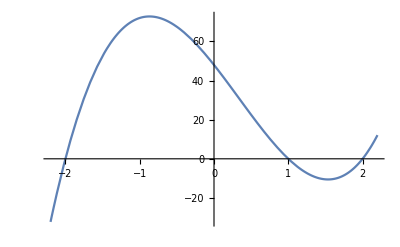

3 x^4-4 x^3-24 x^2+48 x

```mathematica
(x-1)(x+2)(x-2)//Expand;
Integrate[%,x]12//Expand
%//TeXForm
D[%,x]
Solve[%==0,x]
Plot[%%,{x,-2.2,2.2}]
```

#### 3)

```mathematica
(3-2I)/(1+2I)+2/I^3
Solve[z^2-2z+2==0,z]
```

-1/5+(2 ⅈ)/5

{{z→1-ⅈ},{z→1+ⅈ}}

#### 4)

```mathematica
1/(x+1)+3/(x-2)//Together
Numerator[%]/Expand[Denominator[%]]
Integrate[%,x]
%%//TeXForm
```

(2 (1+2 x))/((-1+x) (1+x))

(2 (1+2 x))/(-1+x^2)

3 Log[1-x]+Log[1+x]

\frac{2 (2 x+1)}{x^2-1}

#### 5)

{{x→-1},{x→2}}

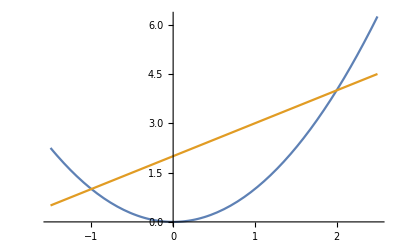

9/2

```mathematica
y1=x^2;
y2=x+2;
Solve[y1==y2,x]
Plot[{y1,y2},{x,-1.5,2.5}]
Integrate[y2-y1,{x,-1,2}]
```

#### 6)

```mathematica
A1={{2,1,1},{-1,1,2},{3,2,-1}}
B1={{3},{-2},{1}};
Solve[A1.{{x},{y},{z}}==B1,{x,y,z}]
```

{{2,1,1},{-1,1,2},{3,2,-1}}

{{x→2,y→-2,z→1}}

#### 7)

0

3

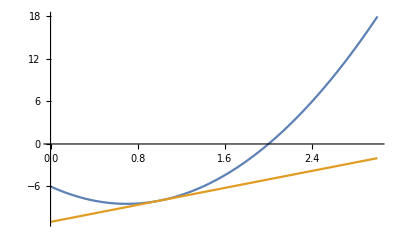

-8+3 (-1+x)

```mathematica
f1[x_]:=5 x^2-7x-6;

x0=1;
f1[2]
f1'[x0]
g1[x_]:=f1'[x0](x-x0)+f1[x0];
Plot[{f1[x],g1[x]},{x,0,3}]
g1[x]
```

#### 8)

```mathematica
y1=-x;
y2=2x;
S=Integrate[(y2-y1),{x,0,2}]
Sy=Integrate[(y2-y1)x,{x,0,2}]
Sx=1/2Integrate[y2^2-y1^2,{x,0,2}]
```

6

8

4